# FaizonZaman/LexicalCases

Extract lexical patterns from text

## Paclet Manifest

"Documentation"

"English"

"Guides"

"LexicalCases.nb"DocumentationEnglishGuidesLexicalCases.nb

"ReferencePages"

"Symbols"

"BoundToken.nb"DocumentationEnglishReferencePagesSymbolsBoundToken.nb

"CountSummaryLowercase.nb"DocumentationEnglishReferencePagesSymbolsCountSummaryLowercase.nb

"DataJoin.nb"DocumentationEnglishReferencePagesSymbolsDataJoin.nb

"ExpandPattern.nb"DocumentationEnglishReferencePagesSymbolsExpandPattern.nb

"FormatLexicalPattern.nb"DocumentationEnglishReferencePagesSymbolsFormatLexicalPattern.nb

"HideMissing.nb"DocumentationEnglishReferencePagesSymbolsHideMissing.nb

"LexicalCases.nb"DocumentationEnglishReferencePagesSymbolsLexicalCases.nb

"LexicalDispersionPlot.nb"DocumentationEnglishReferencePagesSymbolsLexicalDispersionPlot.nb

"LexicalDispersionSmoothHistogram.nb"DocumentationEnglishReferencePagesSymbolsLexicalDispersionSmoothHistogram.nb

"LexicalMap.nb"DocumentationEnglishReferencePagesSymbolsLexicalMap.nb

"LexicalPattern.nb"DocumentationEnglishReferencePagesSymbolsLexicalPattern.nb

"LexicalPatternQ.nb"DocumentationEnglishReferencePagesSymbolsLexicalPatternQ.nb

"LexicalStructure.nb"DocumentationEnglishReferencePagesSymbolsLexicalStructure.nb

"LexicalSummary.nb"DocumentationEnglishReferencePagesSymbolsLexicalSummary.nb

"LexigramCount.nb"DocumentationEnglishReferencePagesSymbolsLexigramCount.nb

"MaxCategories.nb"DocumentationEnglishReferencePagesSymbolsMaxCategories.nb

"OptionalToken.nb"DocumentationEnglishReferencePagesSymbolsOptionalToken.nb

"StopWordQ.nb"DocumentationEnglishReferencePagesSymbolsStopWordQ.nb

"SynonymToken.nb"DocumentationEnglishReferencePagesSymbolsSynonymToken.nb

"ToLexicalPattern.nb"DocumentationEnglishReferencePagesSymbolsToLexicalPattern.nb

"TypeToken.nb"DocumentationEnglishReferencePagesSymbolsTypeToken.nb

"WordToken.nb"DocumentationEnglishReferencePagesSymbolsWordToken.nb

"$FilterableProperties.nb"DocumentationEnglishReferencePagesSymbols$FilterableProperties.nb

"$LexicalCasesServices.nb"DocumentationEnglishReferencePagesSymbols$LexicalCasesServices.nb

"$SampleParagraph.nb"DocumentationEnglishReferencePagesSymbols$SampleParagraph.nb

"$SampleSentence.nb"DocumentationEnglishReferencePagesSymbols$SampleSentence.nb

"$SampleStringExpression.nb"DocumentationEnglishReferencePagesSymbols$SampleStringExpression.nb

"Tutorials"

"LexicalCasesOverview.nb"DocumentationEnglishTutorialsLexicalCasesOverview.nb

"Kernel"

"Abstractions.wl"KernelAbstractions.wl

"LexicalCases.wl"KernelLexicalCases.wl

"LexicalPattern.wl"KernelLexicalPattern.wl

"Plots.wl"KernelPlots.wl

"Samples.wl"KernelSamples.wl

"Utilities.wl"KernelUtilities.wl

"Validation.wl"KernelValidation.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

"Tests"

"Abstractions.wlt"TestsAbstractions.wlt

"LexicalCases.wlt"TestsLexicalCases.wlt

"LexicalStructure.wlt"TestsLexicalStructure.wlt

"Patterns.wlt"TestsPatterns.wlt

"Utilities.wlt"TestsUtilities.wlt

"Validation.wlt"TestsValidation.wlt

## Web Content

### Headline Image

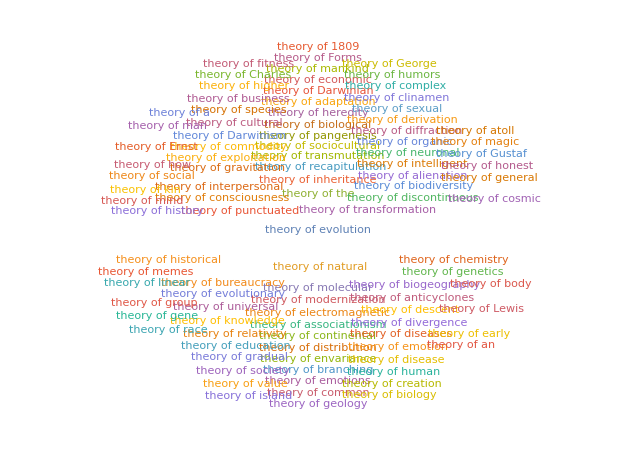

### Basic Description

Search text for lexical patterns. While similar to StringCases, TextCases etc., content types can be used freely in a StringExpression (as opposed to expressing complex lexical patterns in a Containing wrapper). Files, search index objects, and Wikipedia queries are supported. Results are returned in a summary object which supports several subvalues. Consult the documentation for usage.

### Details

This functionality came about when I needed to find adjectives before certain phrases. I initially gathered article text from Wikipedia, then used TextCases and TextContents with the Containing wrapper, (Containing["AdjectivePhrase",Verbatim["music"]] for example), but it turned out to be slow. So I implemented some lexical pattern objects for use in StringExpression's. This way I can search for the string pattern with StringCases.

TextCases is used internally to extract examples of a content type from the source text. These examples then replace the TypeToken in the StringExpression. You can see the lexical pattern generated from a piece of text with ExpandPattern. Note that this means, for example, if you have TypeToken["Adjective"] in your lexical pattern, the token will be replaced by all text snippets identified as adjectives in the source text.

I'd also like to say thanks to Swastik Banerjee for helping me improve SearchIndexObject support!

### Primary Context

FaizonZaman`LexicalCases`

### Main Guide Page

## Examples

```mathematica
Quit[]
```

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Tests

```mathematica
Block[
{tests=PacletExtensionFiles[,"Resource"]//Values/*Flatten},
QuietEcho@TestReport[tests]
]
```

TestReportObject[…]

### Basic Examples

Search for verb phrases beginning with "Alice" in "Alice in Wonderland":

```mathematica
alice=ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
aliceVbAvb=LexicalCases[alice,"Alice "~~TypeToken["Verb"]~~" "~~TypeToken["Adverb"]]
```

LexicalSummary[…]

```mathematica
aliceVbAvb["Dataset"]
```

-Graphics-

```mathematica
aliceVbAvb["CountGroups"]
```

-Graphics-

### Scope

Search for a lexical pattern in Wikipedia articles containing "darwin":

```mathematica
darwin=LexicalCases["Content"->"darwin",BoundToken["theory of"]~~" "~~WordToken[1],MaxItems->1000];
```

```mathematica
darwin["CountGroups"]
```

-Graphics-

Search over index objects:

```mathematica
index = CreateSearchIndex["ExampleData/Text"]
```

-Graphics-

```mathematica
indexResults=LexicalCases[index->All, WordToken[1]~~TypeToken["Verb"]];
```

Visualize the results in a WordCloud:

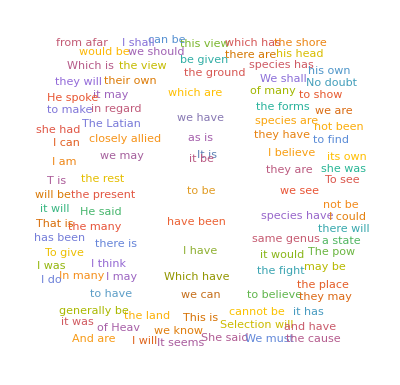

```mathematica
indexResults["WordCloud"]
```

Format a LexicalPattern for labeling:

```mathematica
FormatLexicalPattern["Alice "~~TypeToken["Verb"]~~" "~~TypeToken["Adverb"]]
```

Alice VERB ADVERB

```mathematica
FormatLexicalPattern["Alice "~~SynonymToken["walks"]~~" "~~TypeToken["Adverb"]]
```

Alice walks_syn ADVERB

```mathematica
FormatLexicalPattern["Alice "~~SynonymToken["walks"]~~" "~~OptionalToken[TypeToken["Adverb"]]]
```

Alice walks_syn (ADVERB)

## Source & Additional Information

### Creator

Faizon Zaman

### Source Control Repository

https://github.com/dishmint/LexicalCases

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

lexical cases

string cases

string search

text search

text cases

search

text analysis

text pattern

text pattern matching

pattern matching

lexical pattern

lexical patterns

linguistics

text mining

lexical dispersion

text dispersion

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

I started work on this to find adjectives preceding particular phrases. Initially, I gathered article text from Wikipedia, then searched for the pattern via TextCases and TextContents with the Containing wrapper, (Containing["AdjectivePhrase",Verbatim["music"]] for example). This approach was slow for my needs, so I created some lexical pattern objects which expand to plain text and string patterns to perform the search with StringCases.

Thanks to Swastik Banerjee for helping improve SearchIndexObject support.